Assuming the direction of everything in the original equations.

F_f-f_2=m_2(x^(..))_2, f_1-F_fb=(m_1+m_b)(x^(..))_1
f_2=f_1
x_1-x_2=A_0 sin[ω t+γ]=q_1
(ẋ)_1-(ẋ)_2=A_0 ω cos[ω t+γ]=(q̇)_1
(x^(..))_1-(x^(..))_2=-A_0 ω^2 sin[ω t+γ]=(q^(..))_1
x_1+x_2=q_2
x_1-x_2=q_1

(q^(..))_1=(f_1-F_fb)/(m_1+m_b)-(F_f-f_1)/m_2=-ω^2 A_0 sin[ω t+γ]

```mathematica
Clear[A,B,m1,m2,mb,m,A0,ω,g,μ,f,ϕ,λ1,λ2,A0,γ]
```

```mathematica
Solve[-(Ff-f)/m2+(f-Fb)/(m1+mb)==-A0 ω^2 Sin[ω t+γ],f]
```

{{f→(Ff m1+Fb m2+Ff mb-A0 m1 m2 ω^2 Sin[γ+t ω]-A0 m2 mb ω^2 Sin[γ+t ω])/(m1+m2+mb)}}

```mathematica
s=FullSimplify[%]
```

{{f→(Fb m2+Ff (m1+mb)-A0 m2 (m1+mb) ω^2 Sin[γ+t ω])/(m1+m2+mb)}}

(q^(..))_2=(F_f-f_1)/m_2+(f_1-F_fb)/(m_1+m_b)

```mathematica
(Ff-f)/m2+(f-Fb)/(m1+mb)/.s
```

{(Ff-(Fb m2+Ff (m1+mb)-A0 m2 (m1+mb) ω^2 Sin[γ+t ω])/(m1+m2+mb))/m2+(-Fb+(Fb m2+Ff (m1+mb)-A0 m2 (m1+mb) ω^2 Sin[γ+t ω])/(m1+m2+mb))/(m1+mb)}

```mathematica
FullSimplify[%]
```

{(-2 Fb+2 Ff+A0 (m1-m2+mb) ω^2 Sin[γ+t ω])/(m1+m2+mb)}

(q^(..))_2=(2 (-F_b+F_f)+A_0 (m_1-m_2+m_b) ω^2 sin[t ω+γ])/(m_1+m_2+m_b)
F_fb=m_b g μ 
F_f=(m_2+2 m_1)g μ
(q^(..))_2=(2 (-m_bg μ +(m_2+2 m_1)g μ)+A_0 (m_1-m_2+m_b) ω^2 sin[t ω+γ])/(m_1+m_2+m_b)

```mathematica
FullSimplify[(-2 (mb g μ)+2 ((m2+2m1) g μ)+A0 (m1-m2+mb) ω^2 Sin[t ω+γ])/(m1+m2+mb)]
```

(2 g (2 m1+m2-mb) μ+A0 (m1-m2+mb) ω^2 Sin[γ+t ω])/(m1+m2+mb)

(q̇)_2

```mathematica
Integrate[%,t]
```

1/(m1+m2+mb)(2 g (2 m1+m2-mb) t μ-A0 (m1-m2+mb) ω Cos[γ] Cos[t ω]+A0 (m1-m2+mb) ω Sin[γ] Sin[t ω])

```mathematica
FullSimplify[%]
```

(2 g (2 m1+m2-mb) t μ-A0 (m1-m2+mb) ω Cos[γ+t ω])/(m1+m2+mb)

```mathematica
Solve[(A0 (m1-m2+mb) ω Cos[γ])/(m1+m2+mb)+c==0,c]
```

{{c→-(A0 (m1-m2+mb) ω Cos[γ])/(m1+m2+mb)}}

q_2

```mathematica
Integrate[(2 g (2 m1+m2-mb) t μ-A0 (m1-m2+mb) ω Cos[γ+t ω])/(m1+m2+mb),t]
```

1/(m1+m2+mb)(g (2 m1+m2-mb) t^2 μ-A0 (m1-m2+mb) Cos[t ω] Sin[γ]-A0 (m1-m2+mb) Cos[γ] Sin[t ω])

```mathematica
FullSimplify[%]
```

(g (2 m1+m2-mb) t^2 μ-A0 (m1-m2+mb) Sin[γ+t ω])/(m1+m2+mb)

x_1

```mathematica
%+A0 Sin[ω t+γ]
```

A0 Sin[γ+t ω]+(g (2 m1+m2-mb) t^2 μ-A0 (m1-m2+mb) Sin[γ+t ω])/(m1+m2+mb)

```mathematica
FullSimplify[%]
```

(g (2 m1+m2-mb) t^2 μ+2 A0 m2 Sin[γ+t ω])/(m1+m2+mb)

(ẋ)_1

```mathematica
(2 g (2 m1+m2-mb) t μ-A0 (m1-m2+mb) ω Cos[γ+t ω])/(m1+m2+mb)+A0 ω Cos[ω t+γ]
```

A0 ω Cos[γ+t ω]+(2 g (2 m1+m2-mb) t μ-A0 (m1-m2+mb) ω Cos[γ+t ω])/(m1+m2+mb)

```mathematica
FullSimplify[%]
```

(2 (g (2 m1+m2-mb) t μ+A0 m2 ω Cos[γ+t ω]))/(m1+m2+mb)

(ẋ)_1=1/(m1+m2+mb)(2 g (2 m1+m2-mb) t μ+A0 ω (2 m2 Cos[γ]+(m1+m2+mb) Cos[t ω]-(m1-m2+mb) Cos[γ+t ω]))
x_1=(g (2 m1+m2-mb) t^2 μ+2 A0 m2 (t ω Cos[γ]-Sin[γ]+Sin[γ+t ω]))/(m1+m2+mb)

The distance mass b moves in one nudge is x_1 at the first time that (ẋ)_1=0.

```mathematica
Clear[A0,ω,m,m1,m2,g,μ,γ,mr,mb]
```

```mathematica
i=0;
Ai=Reap[While[i<8001,
A0=.05;
ω=2 π 3;
γ=.25π;
m=.03478;
m1=.00358;
m2=m-2 m1;
g=9.81;
μ=.37;
mr=.25m+i.0025 m;
mb=mr;
s1=FindRoot[2 (g (2 m1+m2-mb) t μ+A0 m2 ω Cos[γ+t ω]),{t,.0006}];
τ=t/.s1;
If[τ>1/ω(π/2-γ),
τ=1/ω(π/2-γ);
];
Sow[(g (2 m1+m2-mb) t^2 μ+2 A0 m2 Sin[γ+t ω])/(m1+m2+mb)-(2 A0 m2 Sin[γ])/(m1+m2+mb)/.t->τ];
i++;
];
][[2]][[1]];



i=0;
Bi=Reap[While[i<8001,
A0=.05;
ω=2 π 3;
m=.03478;
m1=.00358;
m2=m-2 m1;;
g=9.81;
μ=.37;
mr=.25m+i.0025 m;
mb=mr+m;
s1=FindRoot[2 (g (2 m1+m2-mb) t μ+A0 m2 ω Cos[γ+t ω]),{t,.0006}];
τ=t/.s1;
If[τ>1/ω(π/2-γ),
τ=1/ω(π/2-γ);
];
Sow[(g (2 m1+m2-mb) t^2 μ+2 A0 m2 Sin[γ+t ω])/(m1+m2+mb)-(2 A0 m2 Sin[γ])/(m1+m2+mb)/.t->τ];
i++;
];
][[2]][[1]];
```

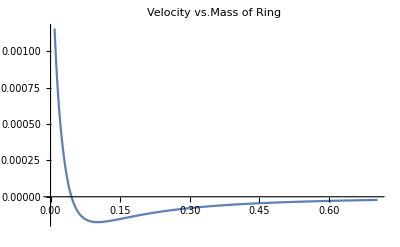

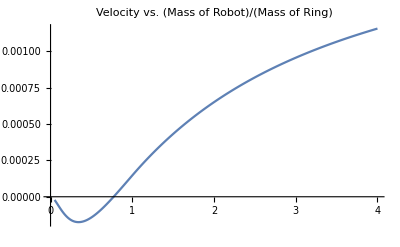

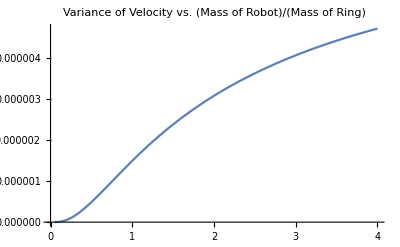

```mathematica
xx={};
xx2={};
xx3={};
xx4={};
xx5={};
i=0;
While[i<Length@Ai,
A0=.05;
ω=2 π 3;
T=90;
f=5;
λ1=.86;
λ2=1-λ1;
m=.03478;
m1=.00358;
m2=m-2 m1;
g=9.81;
μ=.37;
A=Ai[[i+1]];
B=Bi[[i+1]];
ϕ=π/3.8;
AppendTo[xx,{.25m+.0025*i m,-f((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/π}];
AppendTo[xx2,{1/(.25+i*.0025),-f((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/π}];
AppendTo[xx3,{1/(.25+i*.0025),-f/(4 π^3 T)(-4 A B λ1 (1+2 λ1) (π+ϕ-λ1 ϕ)-B^2 λ1 (π^3-6 π λ1+2 π^2 ϕ+6 (-1+λ1) λ1 ϕ)+A^2 (π^3 (-2+λ1)+π (2+4 λ1^2)+2 π^2 ϕ-2 (-1+λ1) (1+2 λ1^2) ϕ)-2 (A-B λ1) (π+ϕ-λ1 ϕ) ((A-B λ1) Cos[2 ϕ]+4 (A-B) λ1 Sin[ϕ])+π^2 (A^2-B^2 λ1) Sin[2 ϕ])}];
i++;
];

ListLinePlot[xx,PlotRange->All,PlotLabel->"Velocity vs.Mass of Ring"]
ListLinePlot[xx2,PlotRange->All,PlotLabel->"Velocity vs. (Mass of Robot)/(Mass of Ring)"]
ListLinePlot[xx3,PlotRange->All,PlotLabel->"Variance of Velocity vs. (Mass of Robot)/(Mass of Ring)"]
```

```mathematica
xx390=xx3;
```

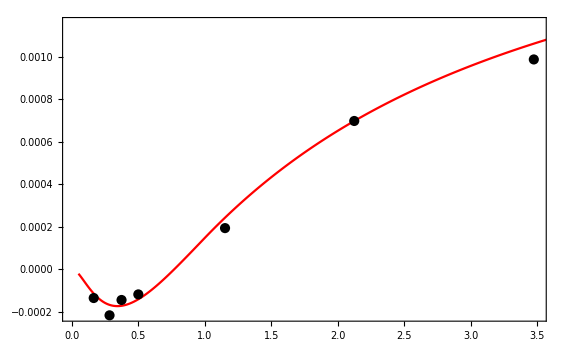

```mathematica
aa=ListLinePlot[xx2,PlotRange->All,PlotStyle->Red];
data={{0.164251208,-0.000136414},{0.283333333,-0.000217871},{0.373626374,-0.000145655},{.5,-0.00011935},{1.152542373,0.000192712},{2.125,0.000696996},{3.476482618,0.000986678}};
bb=ListPlot[data,Joined->False,Mesh->All,PlotStyle->Black];
Show[aa,bb,PlotRange->{{0,3.5},All},Frame->True]
```

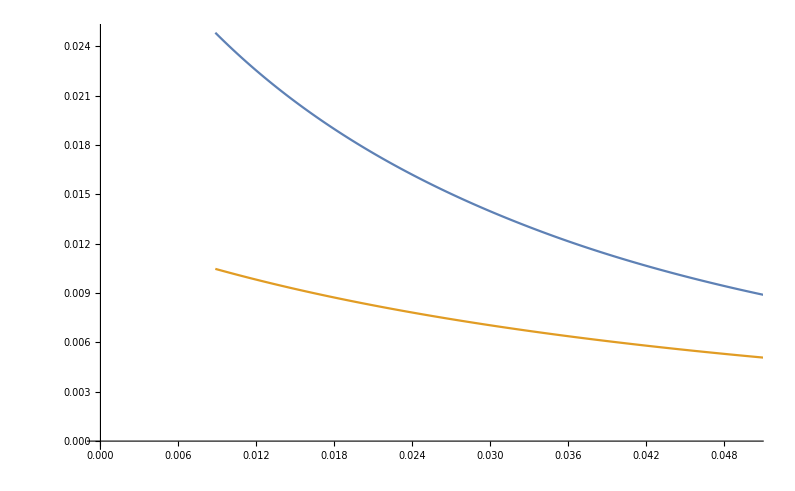

```mathematica
ListLinePlot[{Table[{.25m+.0025*i m,Ai[[i]]},{i,1,Length@Ai}],Table[{.25m+.01*i m,Bi[[i]]},{i,1,Length@Ai}]},PlotRange->(*All*){{0,.05},All}]
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Clear[i]
```

```mathematica
Solve[1/(.25+i*.0025)==3.476482618,i]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{i→15.0588}}

```mathematica
datae={{{0.164251208,-0.000136414},ErrorBar[.000119176]},{{0.283333333,-0.000217871},ErrorBar[.000272568]},{{0.373626374,-0.000145655},ErrorBar[.000422338]},{{.5,-0.00011935},ErrorBar[.000655704]},{{1.152542373,0.000192712},ErrorBar[.00119943]},{{2.125,0.000696996},ErrorBar[.001004625]},{{3.476482618,0.000986678},ErrorBar[.001004625]}};
datae2={{{0.164251208,-0.000136414},ErrorBar[Sqrt[xx3120[[594,2]]]]},{{0.283333333,-0.000217871},ErrorBar[Sqrt[xx3150[[328,2]]]]},{{0.373626374,-0.000145655},ErrorBar[Sqrt[xx3120[[243,2]]]]},{{.5,-0.00011935},ErrorBar[Sqrt[xx3120[[175,2]]]]},{{1.152542373,0.000192712},ErrorBar[Sqrt[xx3120[[62,2]]]]},{{2.125,0.000696996},ErrorBar[Sqrt[xx3120[[22,2]]]]},{{3.476482618,0.000986678},ErrorBar[Sqrt[xx390[[4,2]]]]}};
```

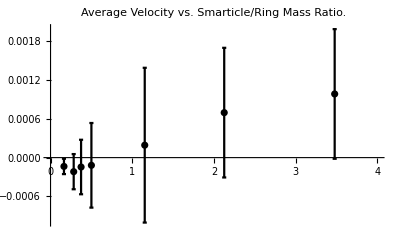

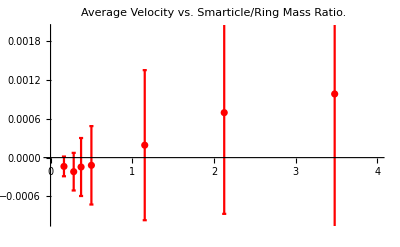

```mathematica
hw=.05;
bbb=ErrorListPlot[datae,PlotStyle->Black,PlotRange->{{0,4},{-.001,.002}},ErrorBarFunction->Function[{coords,errs},{(*the vertical line:*)Line[{coords-{0,errs[[2,1]]},coords+{0,errs[[2,1]]}}],(*horizontal tick 1:*){Black,Thick,Line[{coords-{hw/2,-errs[[2,1]]},coords+{hw/2,errs[[2,1]]}}]},(*horizontal tick 2:*){Black,Thick,Line[{coords-{hw/2,errs[[2,1]]},coords+{hw/2,-errs[[2,1]]}}]}}],PlotRange->{{0,4},{-.001,.002}},PlotStyle->{Black},PlotLabel->"Average Velocity vs. Smarticle/Ring Mass Ratio."]
bb2=ErrorListPlot[datae2,ErrorBarFunction->Function[{coords,errs},{(*the vertical line:*)Line[{coords-{0,errs[[2,1]]},coords+{0,errs[[2,1]]}}],(*horizontal tick 1:*){Red,Thick,Line[{coords-{hw/2,-errs[[2,1]]},coords+{hw/2,errs[[2,1]]}}]},(*horizontal tick 2:*){Red,Thick,Line[{coords-{hw/2,errs[[2,1]]},coords+{hw/2,-errs[[2,1]]}}]}}],PlotRange->{{0,4},{-.001,.002}},PlotStyle->{Red},PlotLabel->"Average Velocity vs. Smarticle/Ring Mass Ratio."]
```

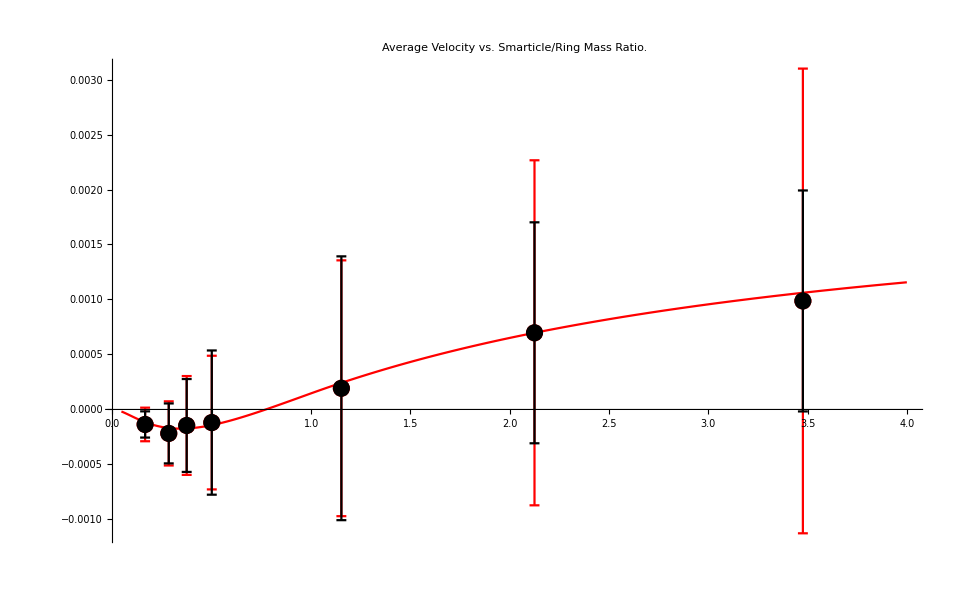

```mathematica
Show[bb2,aa,bbb,PlotRange->All]
```

```mathematica
Sqrt[xx390[[15,2]]]
```

0.00210335

```mathematica
xx390[[15,1]]
```

3.50877